```mathematica
Clear["Global`*"]
MyAdjacencyMatrix[G0_]:=Module[{g=G0},n=Length[VertexList[g]];A=ConstantArray[0,{n,n}];
For[x=1,x≤n,x++,V=VertexList[NeighborhoodGraph[g,x,1]];For[y=1,y≤Length[V],y++,A[[x,V[[y]]]]=1]];
A-IdentityMatrix[n]
]
Smash[G0_,S0_]:=Module[{G=G0,S=S0,V,A,Sbar},
(*Get the adjacency matrix of the graph*)
A=AdjacencyMatrix[G];
V=VertexList[G];
(*Map vertex labels to matrix indices*)
S=Flatten[Position[V,#]&/@S0];
Sbar=Complement[Range[Length[V]],S];
(*Compute the Schur complement formula*)
A[[S,S]]-A[[S,Sbar]].Inverse[A[[Sbar,Sbar]]-L IdentityMatrix[Length[Sbar]]].A[[Sbar,S]]
]
```

```mathematica
(*Full Rank Decomposition Definition*)
Options[FullRankDecomposition]={Method->Automatic,Modulus->0,Tolerance->Automatic,ZeroTest->Automatic};

FullRankDecomposition[m_?MatrixQ,opts:OptionsPattern[]]:=With[{res=iFullRankDecomposition[m,opts]},res/;MatchQ[res,{_?MatrixQ,_?MatrixQ}]]

iFullRankDecomposition[ma_,opts:OptionsPattern[FullRankDecomposition]]:=Module[{m=ma,gf,pos,rank,rref,sig,svd,um,vm},
If[StructuredArray`ContainsSparseOrStructuredArray[m],
m=Normal[m,SparseArray|StructuredArray]];
If[MatrixQ[m,NumericQ]&&Internal`EffectivePrecision[m]<∞,
svd=SingularValueDecomposition[m,FilterRules[Join[{opts},Options[FullRankDecomposition]],Options[SingularValueDecomposition]]];
If[!MatchQ[svd,{__?MatrixQ}],Return[$Failed,Module]];
{um,sig,vm}=svd;
rank=LengthWhile[sig=Diagonal[sig],#!=0&];
{um[[All,1;;rank]],Times[Take[sig,rank],Take[ConjugateTranspose[vm],rank]]},
rref=RowReduce[m,FilterRules[Join[{opts},Options[FullRankDecomposition]],Options[RowReduce]]];
If[!MatrixQ[rref],Return[$Failed,Module]];
pos=Flatten[Position[Transpose[rref],{0...,1,___},1]];
gf=Select[rref,Not@*LinearAlgebra`Private`ZeroVectorQ];
rank=Min[Length[pos],Length[gf]];
{m[[All,Take[pos,rank]]],Take[gf,rank]}]]

(*Helper function to make the Decompositions square*)
FullRankSquareDecomposition[K_?MatrixQ]:=Module[{X,Y,m,n,r,s,Xsq,Ysq},
{X,Y}=FullRankDecomposition[K];
{m,r}=Dimensions[X];
{s,n}=Dimensions[Y];

(*Pad X to m×m by adding (m−r) zero columns*)
Xsq=ArrayPad[X,{{0,0},{0,m-r}}];

(*Pad Y to m×n by adding (m−r) zero rows*)
Ysq=ArrayPad[Y,{{0,m-r},{0,0}}];

{Xsq,Ysq}
]

(*Helper function to remove the zero row/column added in extraneously from the square rank decomposition*)
RemoveAllZeroRowColumnPairs[m_?MatrixQ]:=Module[{n,zeroIndices,keepIndices},
n=Length[m];

zeroIndices=Select[Range[n],
Total[Abs[m[[#,All]]]]==0&&Total[Abs[m[[All,#]]]]==0&
];

keepIndices=Complement[Range[n],zeroIndices];

m[[keepIndices,keepIndices]]
]

(*Partial Fraction Decomposition for Matrices*)
ApartMatrix[m_] := Apart /@ m
```

```mathematica
(*Helper function to identify the M zero block from Lemma 3.3*)
SplitByTopLeftSquareZeroBlock[M_?MatrixQ]:=Module[{rows,cols,r=0,c=0,maxR,maxC,isZeroBlockQ,found=False},
{rows,cols}=Dimensions[M];

(*Helper function to test top-left r×r block for all zeros*)isZeroBlockQ[r_]:=Total[Abs[Flatten[M[[1;;r,1;;r]]]]]==0;

(*Find max r such that top-left r×r block is zero*)
Do[
If[isZeroBlockQ[i],
r=i;
found=True
],
{i,Min[rows,cols]}  (*check only up to the minimum dimension for square blocks*)
];

If[!found,Return["No square top-left zero block found"]];

{
M[[1;;r,1;;r]],(*top-left square zero block*)
M[[1;;r,r+1;;cols]],(*top-right B*)
M[[r+1;;rows,1;;r]],(*bottom-left C*)
M[[r+1;;rows,r+1;;cols]]  (*bottom-right D*)
}
]
```

```mathematica
(*Single Step Unfolding Recursive Algorithm see Lemma 3.3*)
UnfoldSingleStep[K_?MatrixQ,ν_?NumericQ,1]:=Module[{X,Y,m1,n1,m2,n2,A},
(*Using square decomposition for now - TODO: Simplify to dimensions of largest rank*)
{X,Y}=FullRankSquareDecomposition[K];
{m1,n1}=Dimensions[Y];
{m2,n2}=Dimensions[X];
A=ArrayFlatten[{{ConstantArray[0,{m2,n1}],X},{Y,ν*IdentityMatrix[n2]}}];

(*Remove all zero row column pairs from extraneous square decomposition*)
RemoveAllZeroRowColumnPairs[A]
]

UnfoldSingleStep[K_?MatrixQ,ν_?NumericQ,n_]:=Module[{X,Y,M,C,D,F,A,mat,m1,n1,m2,n2,m3,n3,m4,n4},

(*Using square decomposition for now - TODO: Simplify to dimensions of largest rank*)
{X,Y}=FullRankSquareDecomposition[K];
(*Recursive Step Backwards*)
A= UnfoldSingleStep[X, ν, n-1];
{M,C,D,F} = SplitByTopLeftSquareZeroBlock[A];

(*Construct next level Matrix*)
{m1,n1}=Dimensions[Y];
{m2,n2}=Dimensions[X];
{m3,n3}=Dimensions[C];
{m4,n4}=Dimensions[D];
mat = ArrayFlatten[{
{ConstantArray[0,{m3,n1}], ConstantArray[0,{m3,n4}], C},
{Y, ν * IdentityMatrix[m1], ConstantArray[0,{m1,n3}]},
{ConstantArray[0,{m4,n1}],D,F}
}];

(*Remove all zero row column pairs from extraneous square decomposition*)
RemoveAllZeroRowColumnPairs[mat]
]
```

```mathematica
(*Convert addition to list*)
extractAdditiveTerms[expr_]:=If[Head[expr]===Plus,List@@expr,{expr}];

(*Remove all constant entries*)
RemoveConstants[list_,var_]:=Select[list,Not[FreeQ[#,var]]&]

(*Helper function to extract coeffs*)
ExtractPartialFractionCoefficients[mat_,var_]:=Module[{terms,uniqueTerms,coeffMatrices,shape,flattenExprs,termMatchQ,coeffForTerm, varTerms, constantTerm},

shape=Dimensions[mat];

(*Step 1:Flatten all expressions and collect all partial terms*)flattenExprs=Flatten[extractAdditiveTerms/@Flatten[mat]];
flattenExprs = RemoveConstants[flattenExprs, var];

(*Step 2:Normalize each term by dividing by its coefficient*)terms=DeleteDuplicates[NormalizeTerm[#]&/@flattenExprs];

(*Step 3:Create a coefficient matrix for each term*)coeffForTerm[term_]:=Module[{extractCoeff},
extractCoeff[expr_]:=Module[{terms,matches},
(*Ensure each entry is a list*)
terms=If[Head[expr]===Plus,List@@expr,{expr}];

(*Quiet suppresses harmless warnings from Simplify*)
(*Select only keeps terms that simplify to scalar multiples of the input term*)
matches=Select[terms,Quiet[Simplify[#/term]=!=0&&FreeQ[Simplify[#/term],var]]&];

(*Total adds up all such scalar multiples*)
Total[Quiet[Simplify[#/term]&/@matches]]];
Map[extractCoeff,mat,{2}]
];

(*Step 4:Assemble result as Association*)
varTerms = AssociationThread[terms,coeffForTerm/@terms];

(*Step 5:Calculate constant portion of matrix*)
constantTerm = mat - Total[KeyValueMap[#1 #2 &, varTerms]];

{constantTerm,  varTerms}
]

NormalizeTerm[expr_]:=Module[{num,den,c},
{num,den}={Numerator[expr],Denominator[expr]};
c=First@Cases[num,_?NumericQ,{0,Infinity},1]/. {}->1;(*scalar*)
Together[(num/c)/den]
];

(*Heleper function to get the shifted ν part of the denominator*)
getDenomOffset[expr_,x_]:=Module[{den,shifted},
den=Denominator[expr];
shifted=Cases[expr,
Power[sum_/;MatchQ[sum,a_+x]&&FreeQ[sum[[1]],x],n_.]:>{sum[[1]],n},{0,Infinity}
];
If[shifted==={},
0,
First[shifted]
]
];

(*Helper function to get the power k of each denominator*)
getDenomPower[expr_,x_]:=Module[{den, y},
den=Denominator[Together[expr]];
Replace[den,
{Power[sum_,n_.]/;MatchQ[sum,a_+b_]&&(FreeQ[a,x]||FreeQ[b,x]):>n,
sym_Symbol/;sym===x:>1  (*Handle x as x^1*)}
]
];
```

{{0,0,1},{0,0,1},{1,1,0}}

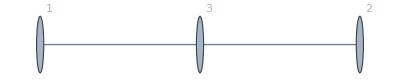

{{1/L,1/L},{1/L,1/L}}

```mathematica
(*2x2 all 1's case with n = 1 for Lemma 3.3*)
A = UnfoldSingleStep[{{1,1},{1,1}}, 0, 1]
G = AdjacencyGraph[A, VertexLabels->"Name"]
Smash[G,{1,2}]
```

{{0,0,0,1},{0,0,1,0},{1,0,0,0},{0,1,0,0}}

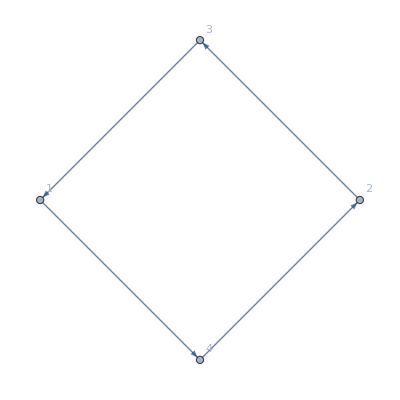

{{0,1/L},{1/L,0}}

```mathematica
(*2x2 with 1's on off diagonal case with n = 1 for Lemma 3.3*)
(*Results in a directed graph - non-hermitian I guess?*)
A = UnfoldSingleStep[{{0,1},{1,0}}, 0, 1]
G = AdjacencyGraph[A, VertexLabels->"Name"]
Smash[G,{1,2}]
```

{{0,0,0,1},{0,0,0,1},{1,1,0,0},{0,0,1,0}}

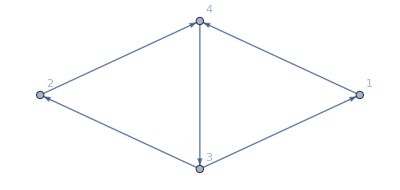

(1/L^2 | 1/L^2
1/L^2 | 1/L^2)

```mathematica
(*Test Single Step with higher powers of n*)
(*2x2 all 1's case with n = 2 for Lemma 3.3*)
A = UnfoldSingleStep[{{1,1},{1,1}}, 0, 2]
G = AdjacencyGraph[A, VertexLabels->"Name"]
MatrixForm[Smash[G,{1,2}]]
```

```mathematica
mat={{1/(x (x+1)),(x+1)/(x^2-1)},{1/(x^2+x),x/(x^2-1)}};

apartmat = ApartMatrix[mat]
```

{{1/x-1/(1+x),1/(-1+x)},{1/x-1/(1+x),1/(2 (-1+x))+1/(2 (1+x))}}

```mathematica
(*Test Partial Fractions*)
mat={{1/x-1/(x+1)^2,2/x+3/(x+1)+5},{1,5/(x+1)}}

{M, varTerms} = ExtractPartialFractionCoefficients[ApartMatrix[mat],x]

A = mat + Total[KeyValueMap[Function[{k,v},
Module[{ν,n,U},
ν=getDenomOffset[k,x];
Print["Offset"];
Print[ν];
n=getDenomPower[k,x];
Print["Power"];
Print[n];
Print["Coefficient"];
Print[k];
Print["Coefficient Matrix"];
Print[v];
U=UnfoldSingleStep[v,ν,n];
Print["U"];
Print[U];
U
]
]
,varTerms
]
]
```

{{1/x-1/(1+x)^2,5+2/x+3/(1+x)},{1,5/(1+x)}}

{{{0,5},{1,0}},<|1/x→{{1,2},{0,0}},1/(1+x)^2→{{-1,0},{0,0}},1/(1+x)→{{0,3},{0,5}}|>}

Offset

0

Power

1

Coefficient

1/x

Coefficient Matrix

{{1,2},{0,0}}

U

{{0,0,1},{0,0,0},{1,2,0}}

Offset

{1,1}

Power

2

Coefficient

1/(1+x)^2

Coefficient Matrix

{{-1,0},{0,0}}

U

UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]

Offset

{1,1}

Power

1

Coefficient

1/(1+x)

Coefficient Matrix

{{0,3},{0,5}}

U

UnfoldSingleStep[{{0,3},{0,5}},{1,1},1]

Thread::tdlen: Objects of unequal length in {{1/x-1/(1+x)^2,5+2/x+3/(1+x)},{1,5/(1+x)}}+{{UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]+UnfoldSingleStep[{{0,3},{0,5}},{1,1},1],UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]+UnfoldSingleStep[{{0,3},{0,5}},{1,1},1],1+UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]+UnfoldSingleStep[{{0,3},{0,5}},{1,1},1]},{UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]+«1»,«1»,UnfoldSingleStep[«1»]+«16»[«1»]},«1»} cannot be combined.

{{1/x-1/(1+x)^2,5+2/x+3/(1+x)},{1,5/(1+x)}}+{{UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]+UnfoldSingleStep[{{0,3},{0,5}},{1,1},1],UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]+UnfoldSingleStep[{{0,3},{0,5}},{1,1},1],1+UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]+UnfoldSingleStep[{{0,3},{0,5}},{1,1},1]},{UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]+UnfoldSingleStep[{{0,3},{0,5}},{1,1},1],UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]+UnfoldSingleStep[{{0,3},{0,5}},{1,1},1],UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]+UnfoldSingleStep[{{0,3},{0,5}},{1,1},1]},{1+UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]+UnfoldSingleStep[{{0,3},{0,5}},{1,1},1],2+UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]+UnfoldSingleStep[{{0,3},{0,5}},{1,1},1],UnfoldSingleStep[{{-1,0},{0,0}},{1,1},2]+UnfoldSingleStep[{{0,3},{0,5}},{1,1},1]}}

```mathematica
""
```